## 1300 crustal density, nominal J2

```mathematica
(*Boundary conditions are free surfaces on the top and bottom of finite viscosity layer.*)
```

```mathematica
llist={2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17};
R0=470000;
crust=41860;
comp=400000;
R1=R0-crust;
R2=R0-comp;
surf0=Table[1000,{i,1,17}];
moho0=Table[0,{i,1,17}];
CMB0=Table[0,{i,1,17}];
out=GetTwoLayerEvolutionConst[llist,R0,R1,1300,2434.80,surf0,CMB0,1*^24,0.28381,0.2874,5,2000,False];
```

```mathematica
(6.67408*^-11)(4π)/3((2434.80)*(470000-47670))
(6.67408*^-11)(4π)/3((2160)*(470000))
```

0.287472

0.283813

```mathematica
out
```

GetTwoLayerEvolutionConst[{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},470000,428140,1300,2434.8,{1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},1000000000000000000000000,0.28381,0.2874,5,2000,False]

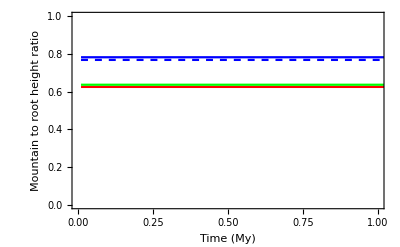

```mathematica
temp14=Table[Table[{5(i-1),-out[[1,i,j]]/out[[2,i,j]]},{i,1,Length@out[[1]]}],{j,2,Length@out[[1,1]]}];
Show[ListPlot[temp14,Joined->True,BaseStyle->{18,FontFamily->"Arial"},Frame->True,FrameStyle->Thick,PlotStyle->{Black,Thick},LabelStyle->Black,PlotRange->{.5,1},FrameLabel->{"Time (My)","Mountain to root height ratio"}],
(*LogPlot[(2440-1380)/1380,{x,.01,250},PlotStyle->Dotted],*)
Plot[(2440-1380)/1380((.289)/0.2838),{x,.01,5000},PlotStyle->Blue],
Plot[(2440-1380)/1380,{x,.01,5000},PlotStyle->{Blue,Dashed}],
Plot[(2440-1380)/1380((470000-46000)/470000)^2,{x,.01,5000},PlotStyle->Red],
Plot[(2440-1380)/1380((470000-46000)/470000)^2(0.289/0.2838),{x,.01,5000},PlotStyle->Green]
]
```

```mathematica
(*Find the point these curves settle out*)
is={};
For[n=1,n≤Length@temp14,n++,
For[i=3,i≤Length@temp14[[n]],i++,
If[Abs[(temp14[[n,i,2]]-temp14[[n,i-1,2]])/temp14[[n,i-1,2]]]≤0.0001,
Print[temp14[[n,i,1]]];
AppendTo[is,i];
Break[];];
];
];
Table[temp14[[n,is[[n]],2]],{n,1,Length@is}]
Length@%
```

{}

0

## Code to get stresses

```mathematica
(*Boundary conditions are free surfaces on the top and bottom of finite viscosity layer.*)
(*Parameters are: 
1. list of SH degrees to evaluate
2. surface radius
3. CMB radius
4. crust density
5. core density
6. list of surface topography in meters starting with n=1
7. list of CMB topography in meters starting with n=1
8. crust viscosity
9. surface gravity
10. step size in My
11. number of steps to run
*)
(*
Returns an array of surface and CMB positions:
{
{{surface height at deg-1 at t1, surface height at deg-2 at t1,...}, 
{surface height at deg-1 at t2, surface height at deg-2 at t2,...},
 ....},
{{CMB height at deg-1 at t1, CMB height at deg-2 at t1,...}, 
{CMB height at deg-1 at t2, CMB height at deg-2 at t2,...},
 ....}
}
*)

GetTwoLayerEvolution4V[llista_,r0_,r2_,ρ0_,ρ2_,h0IN_,h2IN_,η0_,g0_,g2_,tint_,steps_,verbose_]:=(
Block[{initialsurface,initialCMB,surfaces,CMBs,n,output,ηN,ρN,MIsRHS,MIs,RHS,G},
G=6674*^-14;
Clear[h0,h2];
initialsurface=h0IN;
initialCMB=h2IN;

Print["Computing evolution for SH degrees " <> ToString[llista]<> " for " <> ToString[steps]<> " steps of "<> ToString[tint]<> " My each."];

surfaces={initialsurface};
CMBs={initialCMB};
MIsRHS=GetTwoLayerMatrices4V[llista,r0,r2,ρ0,ρ2,η0,g0,g2,verbose];
MIs=MIsRHS[[1]];
RHS=MIsRHS[[2]];
n=1;
While[n≤steps,
If[verbose,
Print["Running step " <> ToString[n]];
];
output=Table[If[MemberQ[llista,i],
Flatten[((MIs[[i]]/.{h0->initialsurface[[i]],h2->initialCMB[[i]]}).(RHS[[i]]/.{h0->initialsurface[[i]],h2->initialCMB[[i]]}))]
,
{0,0,0,0}
]
,
{i,1,Max@llista}];

initialsurface=Table[initialsurface[[i]]+output[[i,1]](3.15576*^7*10^6*tint),{i,1,Length@initialsurface}];
initialCMB=Table[initialCMB[[i]]+output[[i,3]](3.15576*^7*10^6*tint),{i,1,Length@initialCMB}];
AppendTo[surfaces,initialsurface];
AppendTo[CMBs,initialCMB];
n++;
];
Return[{surfaces,CMBs}];
];
);
```

```mathematica
(*Boundary conditions are free surfaces on the top and bottom of finite viscosity layer.*)
(*Note this function and GetTwoLayerEvolution4V have the same input parameters EXCEPT for the extra final parameter r_Arb*)
(*Parameters are: 
1. list of SH degrees to evaluate
2. surface radius
3. CMB radius
4. crust density
5. core density
6. list of surface topography in meters starting with n=1
7. list of CMB topography in meters starting with n=1
8. crust viscosity
9. surface gravity
10. step size in My
11. number of steps to run
12. r_Arb (radius at which stress is evaluated)
*)
(*
Returns an array (length 3) of stresses and pressure at r_Arb:
{
{{Subscript[τ, rr](Subscript[r, Arb],Subscript[t, 1],N=1),Subscript[τ, rr](Subscript[r, Arb],Subscript[t, 1],N=2),...},{Subscript[τ, rr](Subscript[r, Arb],Subscript[t, 2],N=1),Subscript[τ, rr](Subscript[r, Arb],Subscript[t, 2],N=2),...},...},
{{Subscript[τ, rθ](Subscript[r, Arb],Subscript[t, 1],N=1),Subscript[τ, rθ](Subscript[r, Arb],Subscript[t, 1],N=2),...},{Subscript[τ, rθ](Subscript[r, Arb],Subscript[t, 2],N=1),Subscript[τ, rθ](Subscript[r, Arb],Subscript[t, 2],N=2),...},...},
{{Subscript[P, non-hydro](Subscript[r, Arb],Subscript[t, 1],N=1),Subscript[P, non-hydro](Subscript[r, Arb],Subscript[t, 1],N=2),...},{Subscript[P, non-hydro](Subscript[r, Arb],Subscript[t, 2],N=1),Subscript[P, non-hydro](Subscript[r, Arb],Subscript[t, 2],N=2),...},...},
}
*)

GetTwoLayerStresses4V[llista_,r0_,r2_,ρ0_,ρ2_,h0IN_,h2IN_,η0_,g0_,g2_,tint_,steps_,verbose_,rArb_]:=(
Block[{initialsurface,initialCMB,surfaces,CMBs,n,output,ηN,ρN,MIsRHS,MIs,RHS,cmbvector,surfvector,G,Pa,stresses,Arbvector,τrrs,τrθs,Ps},
G=6674*^-14;
Clear[h0,h2];
initialsurface=h0IN;
initialCMB=h2IN;
Print["Computing evolution for SH degrees " <> ToString[llista]<> " for " <> ToString[steps]<> " steps of "<> ToString[tint]<> " My each."];

surfaces={initialsurface};
CMBs={initialCMB};
τrrs={};
τrθs={};
Ps={};
MIsRHS=GetTwoLayerMatrices4V[llista,r0,r2,ρ0,ρ2,η0,g0,g2,verbose];
MIs=MIsRHS[[1]];
RHS=MIsRHS[[2]];

Pa=GetPropagator4V[r0,r2,rArb];
n=1;
While[n≤steps,
If[verbose,
Print["Running step " <> ToString[n]];
];
output=Table[If[MemberQ[llista,i],
Flatten[((MIs[[i]]/.{h0->initialsurface[[i]],h2->initialCMB[[i]]}).(RHS[[i]]/.{h0->initialsurface[[i]],h2->initialCMB[[i]]}))]
,
{0,0,0,0}
]
,
{i,1,Max@llista}];
cmbvector=
Table[If[MemberQ[llista,i],
{output[[i,1]],
output[[i,2]],
-(ρ2-ρ0)*g2*initialCMB[[i]]*r2/η0+((ρ2-ρ0)/ρ0)(4π*G*ρ0*r2)/((2i+1)η0) (r2*initialCMB[[i]]*(ρ2-ρ0)+r0(r2/r0)^i*initialsurface[[i]]*ρ0),
0
}
,
{0,0,0,0}
]
,
{i,1,Max@llista}];
Arbvector=Table[If[MemberQ[llista,i],
(Pa/.{l->i}).Transpose[{cmbvector[[i]]}],
{{0},{0},{0},{0}}]
,{i,1,Max@llista}];
AppendTo[τrrs,Table[η0/rArb Arbvector[[i,3,1]],{i,1,Length@Arbvector}]];
AppendTo[τrθs,Table[η0/rArb Arbvector[[i,4,1]],{i,1,Length@Arbvector}]];
AppendTo[Ps,Table[-(4η0)/rArb Arbvector[[i,1,1]]+(2η0*i(i+1))/rArb Arbvector[[i,2,1]]-Arbvector[[i,3,1]],{i,1,Length@Arbvector}]];
initialsurface=Table[initialsurface[[i]]+output[[i,1]](3.15576*^7*10^6*tint),{i,1,Length@initialsurface}];
initialCMB=Table[initialCMB[[i]]+output[[i,3]](3.15576*^7*10^6*tint),{i,1,Length@initialCMB}];
AppendTo[surfaces,initialsurface];
AppendTo[CMBs,initialCMB];
n++;
];
Return[{τrrs,τrθs,Ps}];
];
);
```

```mathematica
(*Parameters are: 
1. list of SH degrees to evaluate
2. surface radius
3. CMB radius
4. crust density
5. core density
6. list of surface topography in meters starting with n=1
7. list of CMB topography in meters starting with n=1
8. crust viscosity
9. surface gravity
10. step size in My
11. number of steps to run
*)


GetTwoLayerMatrices4V[llista_,r0a_,r2a_,ρ0a_,ρ2a_,η0a_,g0a_,g2a_,verbose_]:=(
Block[{ν2,ν0,LL,l,ηN,ρN,A,Pa,Pa1,p,pc,i,j,τrra,τrrc,G,M,MIs,RHS,RHSs},
G=6674*^-14;
ν2=Log[r2a/r0a];
ν0=Log[r0a/r0a];
Clear[l];
LL=l(1+l);
ηN=1;
ρN=1;

A={{-2,LL,0,0},{-1,1,0,1/ηN},{12ηN,-6LL*ηN,1,LL},{-6ηN,2(2LL-1)ηN,-1,-2}};
Pa[a_,b_]:=MatrixExp[A(a-b)];
Pa1=Pa[ν0,ν2];
(*define a symbolic array to represent the propagator matrix elements*)
Clear[p,pc];
p=Array[pc,{4,4}];
(*Assign actual values (as a function of l) to the elements of the propagator matrix*)
For[i=1,i≤4,i++,For[j=1,j≤4,j++,pc[i,j]=Pa1[[i,j]];]];
(*define radial stresses on surface and CMB*)
τrra=-ρ0a*g0a*h0*r0a/η0a+(4π*G*ρ0a)/((2l+1)η0a) (r2a^2(r2a/r0a)^l h2*(ρ2a-ρ0a)+r0a^2*h0*ρ0a);
τrrc=-(ρ2a-ρ0a)*g2a*h2*r2a/η0a+((ρ2a-ρ0a)/ρ0a)(4π*G*ρ0a*r2a)/((2l+1)η0a) (r2a*h2*(ρ2a-ρ0a)+r0a(r2a/r0a)^l*h0*ρ0a);
(*write out the matrix equation*)
M={{1,0,-pc[1,1],-pc[1,2]},
{0,1,-pc[2,1],-pc[2,2]},
{0,0,-pc[3,1],-pc[3,2]},
{0,0,-pc[4,1],-pc[4,2]}};
RHS=-Transpose[{{
pc[1,3]*τrrc,
pc[2,3]*τrrc,
pc[3,3]*τrrc+τrra,
pc[4,3]*τrrc
}}];
(*assign values to M and RHS, except h0 and h2*)
MIs=Table[If[MemberQ[llista,i],Inverse[M/.{l->i}],IdentityMatrix[4]],{i,1,Max@llista}];
RHSs=Table[If[MemberQ[llista,i],RHS/.{l->i},{{0},{0},{0},{0}}],{i,1,Max@llista}];
Return[{MIs,RHSs}];
];);

GetPropagator4V[r0a_,r2a_,rArb_]:=(
Block[{ν2,νArb,l,LL,ηN,ρN,A,Pa,Pa1,p,pc,i,j},
ν2=Log[r2a/r0a];
νArb=Log[rArb/r0a];
Clear[l];
LL=l(1+l);
(*single layer with uniform η and ρ*)
ηN=1;
ρN=1;

A={{-2,LL,0,0},{-1,1,0,1/ηN},{12ηN,-6LL*ηN,1,LL},{-6ηN,2(2LL-1)ηN,-1,-2}};
Pa[a_,b_]:=MatrixExp[A(a-b)];
Pa1=Pa[νArb,ν2];
Return[Pa1];
];
)
```

```mathematica
PlotPSDEvolution[evo_]:=(
Module[{color,powerlaw,realceres,toplot},
color=Red;
powerlaw=initialCeresSPG;
realceres=CereskSPG;
toplot=Table[Table[{powerlaw[[n-1,1]],(evo[[1,t,n]]/1000)^2(1/(2n+1))},{n,2,Length@evo[[1,t]],2}],{t,1,Length@evo[[1]],Round[(Length@evo[[1]])/20]}];
Print[Show[
ListLogLogPlot[toplot,AspectRatio->.6,Joined->True,TicksStyle->{Black,Thick},Frame->True,FrameTicksStyle->Black,FrameLabel->{"Wavenumber(km^-1)","Spectral power density (km^2)"},FrameStyle->Thick,LabelStyle->Black,BaseStyle->{24,FontFamily->"Arial"},PlotRange->{{6*^-4,.04},{10^-5,2.7}},PlotStyle->{color},PlotMarkers->{Graphics[{color,Disk[]}],.009}],
ListLogLogPlot[powerlaw,Joined->True,PlotStyle->{Thick,Gray}],
ListLogLogPlot[realceres,Joined->True,PlotStyle->{Thick,Black},PlotMarkers->{Graphics[{Black,Disk[]}],.015}]
]];
];
)

(*Plots topographic evolution as function of time*)
ShowTopoVsTime[evosarray_,stepsize_]:=(
Module[{n,nn,surf,cmb,currentevo,toplotsurf,toplotcmb},
Print["Even degrees 2-20"];
currentevo=evosarray;
toplotsurf={};
toplotcmb={};
For[n=1,n≤(Length@evosarray[[1,1]])/2,n++,
nn=2n;
surf=Table[{(i-1)*stepsize,currentevo[[1,i,nn]]},{i,1,Length@currentevo[[1]],Max[1,Round[(Length@currentevo[[1]])/50]]}];
cmb=Table[{(i-1)*stepsize,currentevo[[2,i,nn]]},{i,1,Length@currentevo[[1]],Max[1,Round[(Length@currentevo[[1]])/50]]}];
AppendTo[toplotsurf,surf];
AppendTo[toplotcmb,cmb];
];
(*Print[Show[
ListLogLinearPlot[toplotsurf,Joined->True,PlotRange->{1.1Min[Transpose[toplotcmb[[1]]][[2]]],1.1Max[Join[Transpose[toplotsurf[[1]]][[2]],Transpose[toplotcmb[[1]]][[2]]]]}],
ListLogLinearPlot[toplotcmb,Joined->True,PlotRange->All]
]];*)
pl1=ListPlot[toplotsurf,Joined->True,PlotRange->{1.1Min[Transpose[toplotcmb[[1]]][[2]]],1.1Max[Join[Transpose[toplotsurf[[1]]][[2]],Transpose[toplotcmb[[1]]][[2]]]]}];
pl2=ListPlot[toplotcmb,Joined->True,PlotRange->All];
pl3=ListPlot[-Transpose@(Last@(out)/First@(out)),Joined->True,PlotRange->All];
Show[pl1,pl2,ImageSize->Large]
Show[pl3,ImageSize->Large]
]
);


FindAnalyticτs[evoarray_,timestep_]:=(
Module[{n,array,f,τ,taus,maxstep},
taus={};
maxstep=0;(*this is where the series crosses real Ceres at deg 4*)
For[i=1,i≤Length@evoarray[[1]],i++,
If[evoarray[[1,i,4]]≥0,maxstep++];
];
Print[maxstep];
(*n is across SH degrees*)
For[n=1,n≤(Length@evoarray[[1,1]])/2,n++,
array=Table[{timestep*(i-1.),Log[evoarray[[1,i,2n]]]},{i,1,maxstep}];
f=FindFit[array,b-a*t,{a,b},t];
AppendTo[taus,f[[1,2]]^-1];
(*Print[Show[ListLogPlot[array],LogPlot[f[[2,2]]-f[[1,2]]t,{t,0,4300}]]];
Print[f];*)
];
Return[taus];
];
);
FindAnalyticτsSymmetricMode[evoarray_,htarget_,timestep_]:=(
Module[{n,array,f,τ,taus,maxstep},
taus={};
maxstep=0;(*this is where the series crosses real Ceres at deg 4*)
For[i=1,i≤Length@evoarray[[1]],i++,
If[evoarray[[1,i,4]]≥htarget,maxstep++];
];
Print[maxstep];
(*n is across SH degrees*)
For[n=1,n≤(Length@evoarray[[1,1]])/2,n++,
array=Table[{timestep*(i-1.),Log[evoarray[[1,i,2n]]]},{i,1,maxstep}];
f=FindFit[array,b-a*t,{a,b},t];
AppendTo[taus,f[[1,2]]^-1];
(*Print[Show[ListLogPlot[array],LogPlot[f[[2,2]]-f[[1,2]]t,{t,0,4300}]]];
Print[f];*)
];
Return[taus];
];
);

FindAnalyticτsAntiSymmetricMode[evoarray_,htarget_,timestep_]:=(
Module[{n,array,f,τ,taus,maxstep},
taus={};
maxstep=0;(*this is where the series crosses real Ceres at deg 4*)
For[i=1,i≤Length@evoarray[[1]],i++,
If[evoarray[[1,i,4]]≥htarget,maxstep++];
];
Print[maxstep];
(*n is across SH degrees*)
For[n=1,n≤(Length@evoarray[[1,1]])/2,n++,
array=Table[{timestep*(i-1.),Log[evoarray[[1,i,2n]]]},{i,maxstep,Length@evoarray[[1]]}];
f=FindFit[array,b-a*t,{a,b},t];
AppendTo[taus,f[[1,2]]^-1];
(*Print[Show[ListLogPlot[array],LogPlot[f[[2,2]]-f[[1,2]]t,{t,0,4300}]]];
Print[f];*)
];
Return[taus];
];
);
```